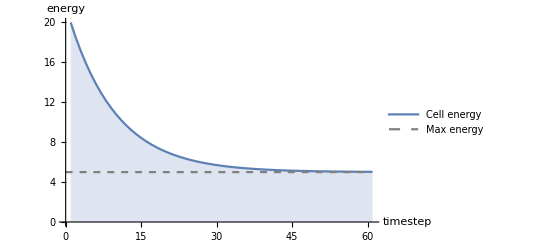

```mathematica
With[{
initialEnergy=20,
maxEnergy=5,
nSteps=60,
rate=0.1
},Show[ListLinePlot[
NestList[#-((#-maxEnergy) rate)&,initialEnergy,nSteps],
PlotRange->All,Filling->Bottom,
AxesLabel->{"timestep","energy"},
PlotLegends->{"Cell energy"}],
Plot[maxEnergy,{x,0,nSteps},
PlotStyle->{Dashed,Gray},
PlotLegends->{"Max energy"}]]
]
```